```mathematica
R:=2
```

```mathematica
x[t_]:=R Cos[t]
```

```mathematica
y[t_]:=R Sin[t]
```

```mathematica
C1[t_]:={x[t],y[t]}
```

```mathematica
C1[0]
```

{2,0}

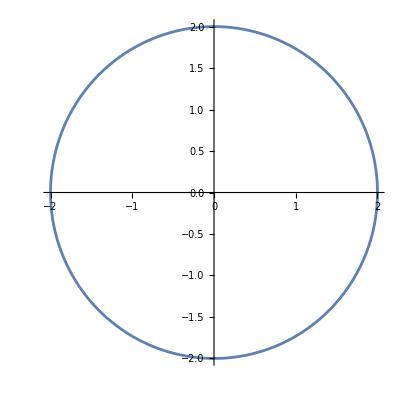

```mathematica
ParametricPlot[C1[t],{t,0,2Pi}]
```

```mathematica
z[t_]:=4
```

```mathematica
C2[t_]:={x[t],y[t],z[t]}
```

```mathematica
ParametricPlot3D[{{0,0,t},C2[t]},{t,0,2Pi}]
```

-Graphics3D-

-Graphics3D-

```mathematica
x1[u_,v_]:=R Cos[u]Sin[v]
```

```mathematica
y1[u_,v_]:=R Sin[u]Sin[v]
```

```mathematica
z1[u_,v_]:=R Cos[v]
```

```mathematica
C3[u_,v_]:={x1[u,v],y1[u,v],z1[u,v]}
```

```mathematica
ParametricPlot3D[C3[u,v],{u,0,2Pi},{v,0,2Pi}]
```

-Graphics3D-

-Graphics3D-

```mathematica
fNormal[x_] := x^2
```

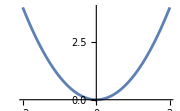

```mathematica
Plot[fNormal[x],{x,-2,2}]
```

```mathematica
fpx[t_]:= t
```

```mathematica
fpy[t_]:= t^2
```

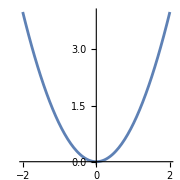

```mathematica
ParametricPlot[ {fpx[t], fpy[t]},{t,-2,2}]
```